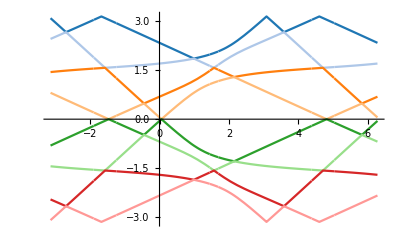

```mathematica
ClearAll["Global`*"]
cd = Cos[d];
sd = Sin[d];
cd2 = cd^2;
sd2 = sd^2;
C0= -4+b^2+c^2+2 b c Sin[d];
C1=24 b cd2 (b-c sd)-48 (-1+c^2) cd2+C0^2;
C2=-432 b^2 (-1+c^2) cd2^2+432 cd2 (b-c sd)^2+72 b cd2 (b-c sd) C0+288 (-1+c^2) cd2 C0+2 C0^3;
C3= (C2+Sqrt[-4 C1^3+C2^2])^(1/3);
C4=C1/(6 2^(2/3) C3)+C3/(12 2^(1/3));
C5= Sqrt[(b^2 cd2)/4-C0/6+C4];
C6 = ((b^3 cd^3)-4 cd (b-c sd)-(b cd C0))/(4 C5);
(*
  Use Re[] to take only the real part for each solution because, while the imaginary part
  should always be zero, the machine precision sometimes yields a small imaginary part.
*)
solns := {
  {p->-ArcCos[Re[(b cd)/4-C5/2-Sqrt[(b^2 cd2)/2-C0/3-C4-C6]/2]]},
  {p->-ArcCos[Re[(b cd)/4-C5/2+Sqrt[(b^2 cd2)/2-C0/3-C4-C6]/2]]},
  {p->-ArcCos[Re[(b cd)/4+C5/2-Sqrt[(b^2 cd2)/2-C0/3-C4+C6]/2]]},
  {p->-ArcCos[Re[(b cd)/4+C5/2+Sqrt[(b^2 cd2)/2-C0/3-C4+C6]/2]]},
  {p-> ArcCos[Re[(b cd)/4+C5/2+Sqrt[(b^2 cd2)/2-C0/3-C4+C6]/2]]},
  {p-> ArcCos[Re[(b cd)/4+C5/2-Sqrt[(b^2 cd2)/2-C0/3-C4+C6]/2]]},
  {p-> ArcCos[Re[(b cd)/4-C5/2+Sqrt[(b^2 cd2)/2-C0/3-C4-C6]/2]]},
  {p-> ArcCos[Re[(b cd)/4-C5/2-Sqrt[(b^2 cd2)/2-C0/3-C4-C6]/2]]}
};

psolns = p/.solns/.{b->0.95, c->0.85};
(* Plot from -Pi to 2 Pi to more clearly show the periodicity *)
Plot[{psolns[[8]], psolns[[7]], psolns[[6]], psolns[[5]],
	psolns[[4]], psolns[[3]], psolns[[2]], psolns[[1]]}, 
	{d, -Pi, 2Pi}, PlotStyle->
      {RGBColor["#1f77b4"],RGBColor["#aec7e8"],RGBColor["#ff7f0e"],RGBColor["#ffbb78"],
       RGBColor["#2ca02c"],RGBColor["#98df8a"],RGBColor["#d62728"],RGBColor["#ff9896"]}]
```